```mathematica
ClearAll["Global`*"];
RunningInteractively=False;(* If running from shell, process must be started from inside same directory in which notebook resides *)
If[Length[$FrontEnd] > 0,RunningInteractively=True];(* If running from the Notebook interface *)
If[RunningInteractively,NBDir=SetDirectory[NotebookDirectory[]]];
<<ManipulatePrepare.m;
FindStableArm;
```

```mathematica
mMaxPlotVal=22;
𝓂EMinMin=-6;
cEMaxPlot=2.7;
PadToLineUpFigsVertically={{30,30},{30,30}};
𝓂EDelEqZeroStyle={Thick,Dashing[{0.02}]};
𝒸Color=Black;𝓂DelEqZeroColor=Red;𝓋Color=Black;RLoStyle={Thin};RHiStyleMove={Blue};RHiStyle=RHiStyleStay={Thick};VerboseOutput=False;PartCost=4;
𝒸PlotRange={{𝓂EMinMin,Automatic},{0,cEMaxPlot}};
𝓋PlotRange={{𝓂EMinMin,Automatic},Automatic};
Get["../../CoreCode/ParametersBase.m"];
Get["../../CoreCode/ParametersBase.m"];Severance=4;𝓂MaxMultiple=6;
𝔤=0.00;
```

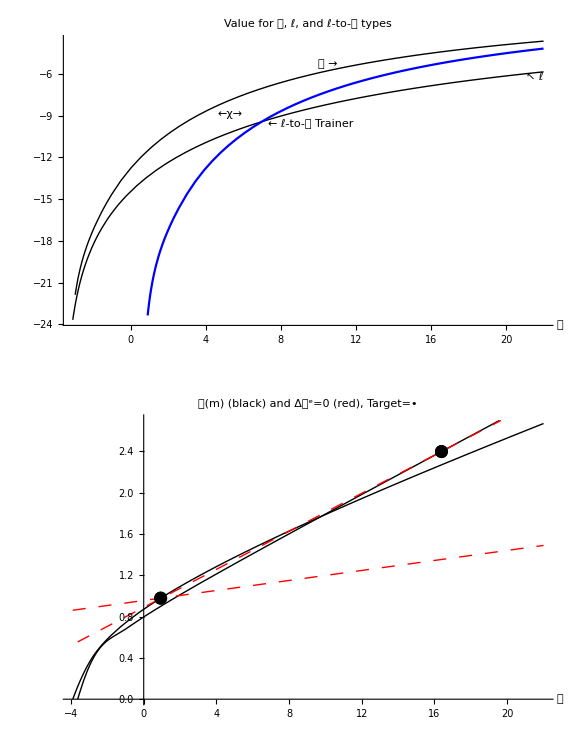

```mathematica
Get["../../CoreCode/ParametersBase.m"];Severance=4;𝓂MaxMultiple=6;
𝔤=0.00;
Get["./PikettyR-FiguresDraw.m"];
ShockWillMakeYouPayToEarnRHi=GraphicsColumn[{vEPlot,cEPlot},Frame->True,ImageSize->Large];
If[RunningInteractively,Print[ShockWillMakeYouPayToEarnRHi]];
```

```mathematica
RunningInteractively=False; Print["Warning:  It takes quite a while to generate the video animation; be patient."];If[RunningInteractively==False,
𝔤List=Table[
Get["../../CoreCode/ParametersBase.m"];Severance=4;𝓂MaxMultiple=6;
𝔤=𝔤Loop;
Get["./PikettyR-FiguresDraw.m"];
GraphicsColumn[{vEPlot,cEPlot},PlotLabel->Column[{"","𝔤="<>ToString[PaddedForm[𝔤,{1,4}]],"𝒷^e="<>ToString[PaddedForm[𝒷E,{2,1}]]}],Frame->True,ImageSize->Large]
    ,{𝔤Loop,𝔤Base,𝔤Base+0.01,0.0001}
];
(* If being viewed in the interactive Notebook interface, show the results *)
If[RunningInteractively,Print[ListAnimate[𝔤List]]];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimateFirstFrame.jpg",𝔤List[[1]]];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimateFirstFrame.pdf",𝔤List[[1]]];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimate.swf",𝔤List];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimate.flv",𝔤List];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimate.mov",𝔤List];
Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimate.avi",𝔤List];Export["/Volumes/Data/Code/Models/Tractable/Latest/EqbmPartial/Mathematica/Examples/ManipulateParameters/PikettyR/Figures/EffectOfGrowthOnTargetListAnimate.gif",𝔤List];
];

Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimateFirstFrame.jpg",𝔤List[[1]]];
Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimateFirstFrame.pdf",𝔤List[[1]]];
Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimate.swf",𝔤List];
Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimate.flv",𝔤List];
(*Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimate.mov",𝔤List];*)
Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimate.avi",𝔤List];Export["/Volumes/Data/Courses/Choice/Questions/BufferStock-PikettyR/LaTeX/EffectOfGrowthOnTargetListAnimate.gif",𝔤List];
```

Warning:  It takes quite a while to generate the video animation; be patient.

```mathematica
ListAnimate[𝔤List]
```

```mathematica
𝔤Manipulate=
Manipulate[Block[{$PerformanceGoal="Quality", 𝔤,𝔤Base},
Get["../../CoreCode/ParametersBase.m"];Severance=4;𝓂MaxMultiple=6;
𝔤=𝔤Loop;
Get["./PikettyR-FiguresDraw.m"];
GraphicsColumn[{vEPlot,cEPlot},Frame->True]]
,{{𝔤Loop,𝔤Base,"𝔤"},𝔤Base,𝔤Base+0.01,(*0.0002*)0.0005,Appearance->"Labeled"}
](*;
(* If being viewed in the interactive Notebook interface, show the results *)
If[RunningInteractively,Print[𝔤Manipulate]];*)
```